```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\mouze\Desktop\CM_labs\lab10\lab10\lab10

```mathematica
test1lim1 =Import["kv_test1_lim1.txt","List"];
test1lim2 = Import["kv_test1_lim2.txt","List"];
test2lim1 = Import["var_2_lim1.txt","List"];
test2lim2 = Import["var_2_lim2.txt","List"];
```

```mathematica
Length@test1lim1
```

201

```mathematica
points1 = Table[{i/(Length@test1lim1 - 1),test1lim1[[i]]},{i,0, Length@test1lim1-1}];
points1lim2 = Table[{0.1 +0.9i/(Length@test1lim2 - 1),test1lim2[[i]]},{i,0, Length@test1lim2-1}];
points2 = Table[{i/(Length@test2lim1 - 1),test2lim1[[i]]},{i,0, Length@test2lim1-1}];
points2lim2 = Table[{0.1 +0.9i/(Length@test1lim2 - 1),test2lim2[[i+1]]},{i,0, Length@test2lim2-1}];
```

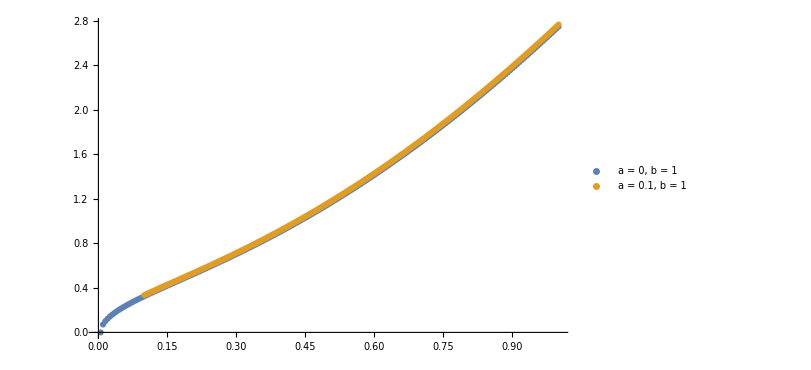

```mathematica
g = ListPlot[{points2, points2lim2},ImageSize->600,PlotLegends->{"a = 0, b = 1", "a = 0.1, b = 1"}]
```

```mathematica
points2[[60]]//N
```

{0.295,1.1155}

```mathematica
points2lim2[[40]]
```

{0.2755,1.06356}

```mathematica
diff = Table[{points2lim2[[i]][[1]],Abs[points2lim2[[i]][[2]] - points2[[i+20]][[2]]] },{i,1,Length@points2lim2-20}];
```

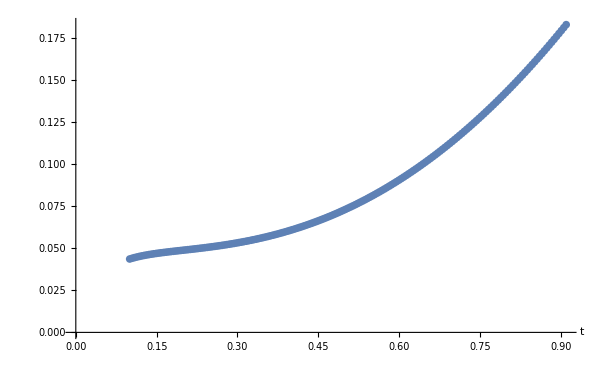

```mathematica
gdiff= ListPlot[diff, ImageSize->600, AxesLabel->{"t"}]
```

```mathematica
f1 = Interpolation[points2]
```

InterpolatingFunction[…]

```mathematica
f2 =  Interpolation[points2lim2]
```

InterpolatingFunction[…]

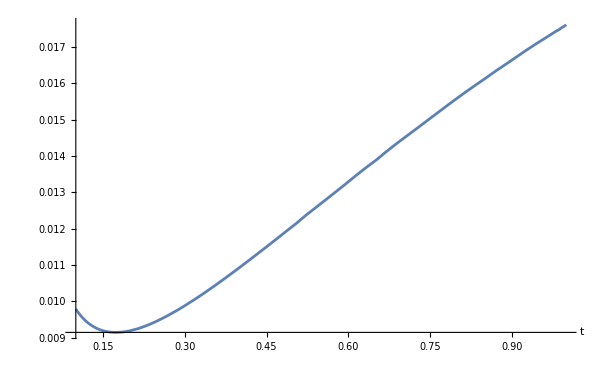

```mathematica
gdiff=Plot[Abs[f1[x] - f2[x]],{x,0.1,1}, ImageSize->600, AxesLabel->{"t"}]
```

```mathematica
Export["test2_kv.jpg", g]
```

test2_kv.jpg

```mathematica
points1lim2[[1]][[2]]
```

0.943372

```mathematica
Export["diff_var_2.jpg",gdiff]
```

diff_var_2.jpg